## Uncontrolled dynamics data generation

```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]]
prm=Association[Import["vaccination_parameters2.json", "JSON"]]
Nstar [l_,s_,e_,is_,ia_,h_,r_]:=l + s + e + is + ia +h + r ;
InfectionForce[l_,s_,e_,is_,ia_,h_,r_]:=
(prm["beta_s"]*is+prm["beta_a"]*ia)/Nstar[l, s, e,is,ia, h, r];
strTheme = "Scientific";
$PlotTheme =strTheme;
ticker[min_,max_,major_,minor_]:=Map[{#,#,{0.02,0}}&,Range[min,max,major]]~Join~Map[{#,""}&,Subdivide[min,max,minor*(max-min)]]
```

/home/gabrielsalcedo/Documentos/UNISON-UADY-Project/programas_240

<|beta_s→0.363282,beta_a→0.251521,epsilon→0.95,var_epsilon→0.1,kappa→0.196078,delta_h→0.2,delta_v→0.00416667,delta_r→0.00555556,p→0.1213,theta→0.2,gamma_a→0.167504,gamma_s→0.0925069,gamma_h→0.119869,mu→0.0000391389,mu_i_s→0.0004,mu_h→0.01632,lambda_v→0.000611352,lambda_l→0.00277778,a_E→0.00841847,a_D→7.25,a_V→1.,c_V→1.,c_T→0.,h_max→9500.,d_final→0.01,coverage→0.2,hospitalization_rate→0.05,d_max→0.000051928,n_pop→2.64464×10^7,T→365,L_0→0.26626,S_0→0.463606,E_0→0.00067033,I_S_0→0.00009283,I_A_0→0.00120986,H_0→0.000134158,R_0→0.266126,D_0→0.00190074,V_0→0.,X_0→0.,X_f→0.2,Y_inc_0→0.122582|>

```mathematica
NCSol = 
NDSolve[
{
(*l'[t]== prm["theta"] * prm["mu"] * Nstar[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]] - (prm["var_epsilon"] * InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]] +prm["lambda_l"]+prm["mu"])*l[t],
s'[t]==(1.0-prm["theta"])*prm["mu"]*Nstar[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]+prm["lambda_l"] * l[t] + prm["delta_r"] * rr[t]-(InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]+prm["mu"])* s[t],*)
l'[t]== 0,
s'[t]==prm["mu"]*Nstar[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]] + prm["delta_r"] * rr[t]-(InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]+prm["mu"])* s[t],
e'[t]==InfectionForce[l[t], s[t], e[t],is[t],ia[t], h[t], rr[t]]*(prm["var_epsilon"]*l[t]+s[t])-(prm["kappa"]+prm["mu"])*e[t],
is'[t]==prm["p"] * prm["kappa"]* e[t]-(prm["gamma_s"]+prm["delta_h"]+prm["mu"])*is[t],
ia'[t]==(1.0-prm["p"])*prm["kappa"]*e[t]-(prm["gamma_a"]+prm["mu"])*ia[t],
h'[t]==prm["delta_h"]*is[t]-(prm["gamma_h"] + prm["mu_h"] + prm["mu"]) * h[t],
rr'[t]==prm["gamma_s"]*is[t] + prm["gamma_a"] * ia[t] + prm["gamma_h"] * h[t]-(prm["delta_r"] + prm["mu"]) * rr[t],
dd'[t]==prm["mu_h"] * h[t],
l[0]==0.0 (*prm["L_0"]*),
s[0]==prm["S_0"] + prm["L_0"],
e[0]==prm["E_0"],
is[0]==prm["I_S_0"],
ia[0]==prm["I_A_0"],
h[0]==prm["H_0"],
rr[0]==prm["R_0"],
dd[0]==prm["D_0"]
},
{l, s, e, is, ia, h,rr,dd},
{t, 0, 360}
];
DataHeader={"time","L","S","E","I_S","I_A","H","R","D"};
NCSol
```

{{l→InterpolatingFunction[…],s→InterpolatingFunction[…],e→InterpolatingFunction[…],is→InterpolatingFunction[…],ia→InterpolatingFunction[…],h→InterpolatingFunction[…],rr→InterpolatingFunction[…],dd→InterpolatingFunction[…]}}

```mathematica
dataWithoutControlSol = Table[
Flatten[
{
t,
Evaluate[{l[t]}/.NCSol],
Evaluate[{s[t]}/.NCSol],
Evaluate[{e[t]}/.NCSol],
Evaluate[{is[t]}/.NCSol],
Evaluate[{ia[t]}/.NCSol],
Evaluate[{h[t]}/.NCSol],
Evaluate[{rr[t]}/.NCSol],
Evaluate[{dd[t]}/.NCSol],
}
],
{t,0,360,0.1}];
cl = Table[
Flatten[
{
t,
Evaluate[{l[t]}/.NCSol] +
Evaluate[{s[t]}/.NCSol] +
Evaluate[{e[t]}/.NCSol] +
Evaluate[{is[t]}/.NCSol] +
Evaluate[{ia[t]}/.NCSol] +
Evaluate[{h[t]}/.NCSol] +
Evaluate[{rr[t]}/.NCSol] +
Evaluate[{dd[t]}/.NCSol]
}
],
{t,0,360,0.1}];
dataNoVacinationSol = Prepend[dataWithoutControlSol, DataHeader];
Export["dataNoControlledDynSol.csv", dataNoVacinationSol];
```

```mathematica
NCSolData =Import[
"dataNoControlledDynSol.csv",
 "Dataset", 
"HeaderLines"->1
];
NCSolData
Dimensions[NCSolData];
plotTime = NCSolData[All,"time"];
nlnvL = NCSolData[[All, "L"]]
nlnvS = NCSolData[[All, "S"]];
nlnvE = NCSolData[[All, "E"]];
nlnvIS = NCSolData[[All, "I_S"]];
nlnvIA = NCSolData[[All, "I_A"]];
nlnvH = NCSolData[[All, "H"]];
nlnvR = NCSolData[[All, "R"]];
nlnvD = NCSolData[[All, "D"]];
tsnlnvL = TimeSeries[Normal[nlnvL], {Normal[plotTime]}];
tsnlnvS = TimeSeries[Normal[nlnvS], {Normal[plotTime]}];
tsnlnvE = TimeSeries[Normal[nlnvE], {Normal[plotTime]}];
tsnlnvIS = TimeSeries[Normal[nlnvIS], {Normal[plotTime]}];
tsnlnvIA = TimeSeries[Normal[nlnvIA], {Normal[plotTime]}];
tsnlnvH = TimeSeries[Normal[nlnvH], {Normal[plotTime]}];
tsnlnvR = TimeSeries[Normal[nlnvR], {Normal[plotTime]}];
tsnlnvD = TimeSeries[Normal[nlnvD], {Normal[plotTime]}];
(*ListLinePlot[tsnlnvH];*)
```

Dataset[<>]

Dataset[<>]

```mathematica
pltNLNVL=ListPlot[
tsnlnvL,
PlotLabel->"Lockdown",
PlotStyle->Red,
PlotRange->{{0,360}, {-0.01,0.1}},
PlotRangeClipping->True,
Frame->True,
PlotTheme->strTheme,
FrameTicks->Automatic,
LabelStyle->Directive[10]
];
pltNLNVS=ListLinePlot[
tsnlnvS,
PlotLabel->"Suceptible",
ImageSize->470,
Filling->Axis,
FrameTicks->{{ticker[0,1,0.1,40],None},{ticker[0,360,120,0.1],None}},
PlotTheme->strTheme
];
```

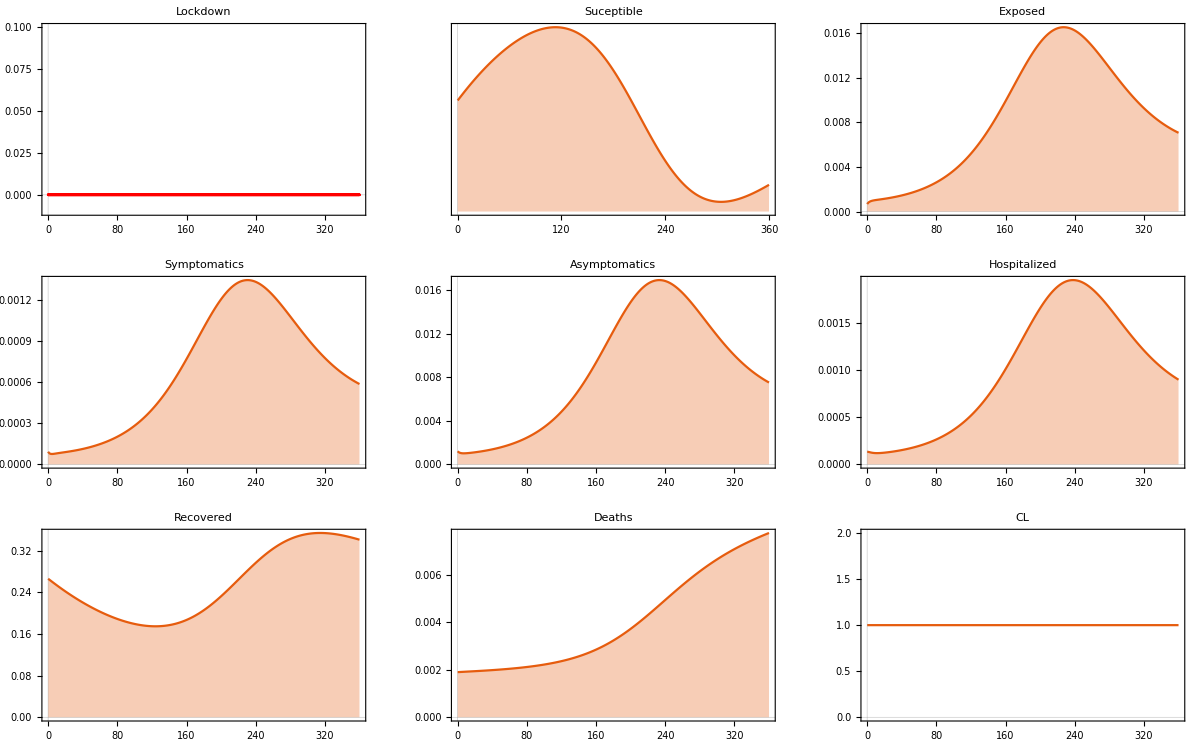

no_contraled_dynamics.pdf

```mathematica
pltNLNVE=ListLinePlot[
tsnlnvE,
PlotRange->All,
PlotLabel->"Exposed",
Filling->Axis,
PlotTheme->strTheme,
FrameTicks->Automatic
];
pltNLNVIS=ListLinePlot[
tsnlnvIS,
PlotRange->All,
PlotLabel->"Symptomatics",
Filling->Axis,
PlotTheme->strTheme,
FrameTicks->Automatic
];

pltNLNVIA=ListLinePlot[
tsnlnvIA,
PlotRange->All,
PlotLabel->"Asymptomatics",
Filling->Axis,
PlotTheme->strTheme,
FrameTicks->Automatic
];
pltNLNVH=ListLinePlot[
tsnlnvH,
PlotRange->All,
PlotLabel->"Hospitalized",
Filling->Axis,
PlotTheme->strTheme,
FrameTicks->Automatic
];
pltNLNVR=ListLinePlot[
tsnlnvR,
PlotRange->All,
PlotLabel->"Recovered",
Filling->Axis,
PlotTheme->strTheme,
FrameTicks->Automatic
];
pltNLNVD=ListLinePlot[
tsnlnvD,
PlotRange->All,
PlotLabel->"Deaths",
Filling->Axis,
PlotTheme->strTheme,
FrameTicks->Automatic
];
pltCL=ListLinePlot[
Thread[{cl[[All,1]], cl[[All,2 ]]}],
(*PlotRange->All,*)
PlotLabel->"CL",
PlotTheme->strTheme,
FrameTicks->Automatic
];

outplot = GraphicsGrid[
{
{pltNLNVL, pltNLNVS, pltNLNVE}, 
{pltNLNVIS, pltNLNVIA, pltNLNVH},
{ pltNLNVR, pltNLNVD, pltCL}
}
]
Export["no_contraled_dynamics.pdf",outplot]
```

```mathematica
ExpandFileName["no_contraled_dynamics.pdf"];
```

Optimal and no optimal controlled dynamics

```mathematica
FNames=FileNames["*.csv"]
Fk[k_]:=Import[FNames[[k]]];
```

{ControlClases.csv,controles_180_720_3000.csv,dataNoControlledDynSol.csv,mejor2.csv,mejor.csv,NoControlClases.csv,ovpEff95Cov80T360.csv,vpEff95Cov80T360.csv}

```mathematica
FNames
```

{ControlClases.csv,controles_180_720_3000.csv,dataNoControlledDynSol.csv,mejor2.csv,mejor.csv,NoControlClases.csv,ovpEff95Cov80T360.csv,vpEff95Cov80T360.csv}

```mathematica
{"ControlClases.csv","controles_180_720_3000.csv","dataNoControlledDynSol.csv","mejor2.csv","mejor.csv","NoControlClases.csv","ovpEff95Cov80T360.csv","vpEff95Cov80T360.csv"}
```

{ControlClases.csv,controles_180_720_3000.csv,dataNoControlledDynSol.csv,mejor2.csv,mejor.csv,NoControlClases.csv,ovpEff95Cov80T360.csv,vpEff95Cov80T360.csv}

```mathematica
AmatC = Fk[1];
ControlSignals = Fk[2];
AmatNC = Fk[6];
Dimensions[AmatC];
Dimensions[AmatNC];
Dimensions[ControlSignals];
tvecC = AmatC[[All,1]];
tvecNC = AmatNC[[All,1]];
tU =ControlSignals[[All, 1]];
xclases={"time","L","S","E","I_S","I_A","H","R","D","V","YIS","YIH","Vcon", "XMAY"};
dim=Length[xclases]
OvDyn = Prepend[AmatC, xclases];
vDyn = Prepend[AmatNC, xclases];
Export["ovpEff95Cov80T360.csv",OvDyn,"csv"];
Export["vpEff95Cov80T360.csv",vDyn,"csv"];
```

14

```mathematica
plotdatC[k_]:= 
ListStepPlot[
Thread[{tvecC,AmatC[[All,k+1]]}],
PlotStyle->{Thick,Blue},
AxesLabel->{"t",xclases[[k]]}
];
plotdatNC[k_]:=
ListStepPlot[
Thread[{tvecNC,AmatNC[[All,k+1]]}],
PlotStyle->{Thick,Red},AxesLabel->{"t",xclases[[k]]},
PlotRange->All];
```

```mathematica
PlotTime=tvecC; 
L = AmatC[[All,2]]; S = AmatC[[All,3]]; Ex = AmatC[[All,4]];
IS =AmatC[[All,5]]; IA = AmatC[[All,6]]; H= AmatC[[All,7]]; 
R = AmatC[[All,8]]; Dcov = AmatC[[All,9]];  V= AmatC[[All,10]];
(*YIS= AmatC[[All,11]]; YIH =  AmatC[[All,12]]; Xcov = AmatC[[All,13]];
XMAY = AmatC[[All,14]];*)
nL = AmatNC[[All,2]]; nS = AmatNC[[All,3]]; nEx = AmatNC[[All,4]];
nIS =AmatNC[[All,5]]; nIA = AmatNC[[All,6]]; nH= AmatNC[[All,7]];
 nR = AmatNC[[All,8]]; nDcov = AmatNC[[All,9]]; nV= AmatNC[[All,10]];
(*nYIS= AmatNC[[All,11]]; nYIH =  AmatNC[[All,12]]; nXcov = AmatNC[[All,13]];
nXMAY = AmatNC[[All,14]];*)
tControl=ControlSignals[[All,1]]; 
uL=prm["lambda_l"]+ ControlSignals[[All,2]];
uV=prm["lambda_v"]+ControlSignals[[All,3]];
doses = 100000 * uV * (L + S + E + IA + R);
lockdownFlux = 100000 *uL * L;
```

```mathematica
Dimensions[AmatC]
```

{362,10}

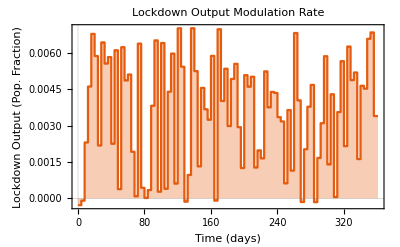

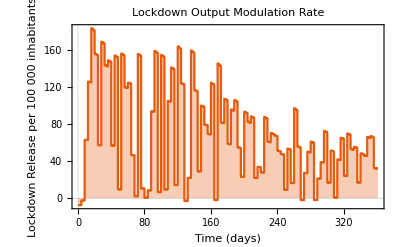

lockdown_control_signal.pdf

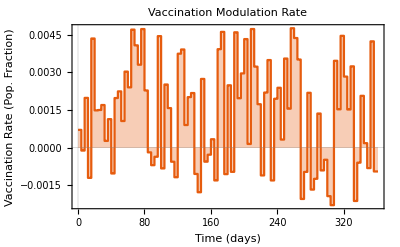

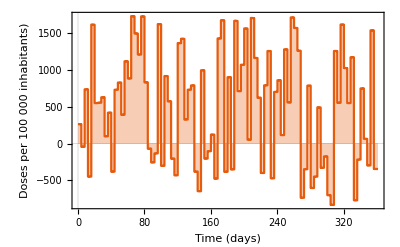

```mathematica
pltuL= 
ListStepPlot[
Thread[{tControl, uL}],
PlotTheme->strTheme,
AxesLabel->{"Time(days)", "Lockdown Input Pop. Fraction"},
Filling->Axis,
PlotRange->All,
PlotLabel->"Lockdown Output Modulation Rate",
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Lockdown Output   (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
]
pltuLF= 
ListStepPlot[
Thread[{tControl, lockdownFlux}],
PlotTheme->strTheme,
AxesLabel->{"Time(days)", "Lockdown Flux per 100 000 inhabitants "},
Filling->Axis,
PlotRange->All,
PlotLabel->"Lockdown Output Modulation Rate",
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Lockdown Release per 100 000 inhabitants",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme,
ImageSize-> 400
]
Export["lockdown_control_signal.pdf",pltuL]
pltuV= 
ListStepPlot[
Thread[{tControl, uV}],
PlotTheme->strTheme,
Filling->Axis,
PlotLabel->"Vaccination Modulation Rate",
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Vaccination Rate (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
]
Export["Vaccination_control_signal.pdf",pltuV];
pltuDoses= 
ListStepPlot[
Thread[{tControl, doses}],
Filling->Axis,
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Doses per 100 000 inhabitants)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme, 
ImageSize-> 400
(*PlotRange->All*)
]
Export["VaccineDosis_control_signal.pdf",pltuDoses];
```

```mathematica
(*TODO: implement coverage*)
```

```mathematica
pltnL =
ListStepPlot[
Thread[{tvecNC,nL}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Lockdown Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
(*PlotRange->{{0,365}, {0.0, 0.6}}*)
];
pltL =
ListStepPlot[
Thread[{tvecC,L}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Lockdown Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltNLNVncL =
ListStepPlot[
{
tsnlnvL,
Thread[{tvecNC,nL}],
Thread[{tvecC,L}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Lockdown Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Lockdown Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
ImageSize->400
];
```

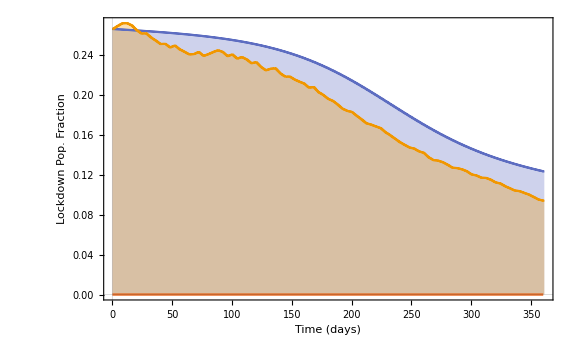

```mathematica
Show[pltNLNVncL,ImageSize->Large]
```

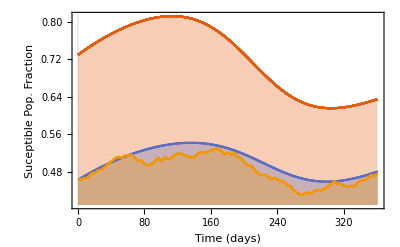

```mathematica
pltnS =
ListStepPlot[
Thread[{tvecNC,nS}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Suceptible Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
	FrameTicks->All,
PlotRange->{{0,360}, {0.0, 0.9}},
PlotTheme->strTheme,
FrameTicks->Automatic
];
pltS =
ListStepPlot[
Thread[{tvecC,S}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Suceptible Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltNLNVncS =
ListStepPlot[
{
tsnlnvS,
Thread[{tvecC,nS}],
Thread[{tvecC,S}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Suceptible Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotTheme->strTheme,
ImageSize->400
]
```

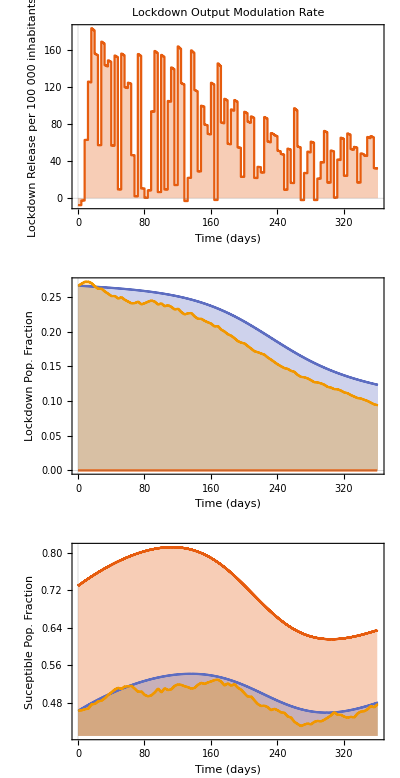

LockdownEffect.pdf

```mathematica
FigLocDownEffect=GraphicsGrid[
{
{pltuLF},
{pltNLNVncL},
{pltNLNVncS}
}
]
Export["LockdownEffect.pdf",FigLocDownEffect]
```

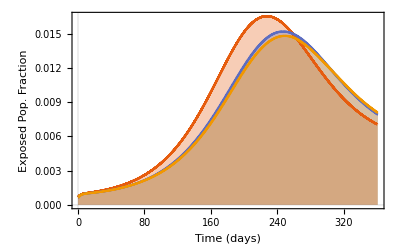

```mathematica
pltnE =
ListStepPlot[
Thread[{tvecNC,nEx}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Exposed Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Exposed (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotRange->{{0,360}, {0.0, 0.9}},
PlotTheme->strTheme
];
pltE =
ListStepPlot[
Thread[{tvecC,E}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Exposed Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Suceptible (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltNLNVncE =
ListStepPlot[
{
tsnlnvE,
Thread[{tvecC,nEx}],
Thread[{tvecC,Ex}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Exposed Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Exposed Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotTheme->strTheme
]
```

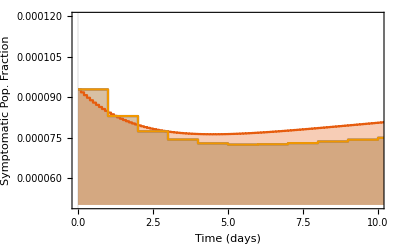

```mathematica
pltnIS =
ListStepPlot[
Thread[{tvecNC,nIS}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Symptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Symptomatic (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme,
PlotRange->{{330,340}, {0.0, 0.0019}}
];
pltIS =
ListStepPlot[
Thread[{tvecC,IS}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Symptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Symptomatic (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme,
PlotRange->{{330,340}, {0.0, 0.0019}}
];
pltNLNVncIS =
ListStepPlot[
{
tsnlnvIS,
Thread[{tvecC,nIS}],
Thread[{tvecC,IS}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Symptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Symptomatic Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotTheme->strTheme,
ImageSize->400,
PlotRange->{{0,10}, {0.00005, 0.00012}}
]
```

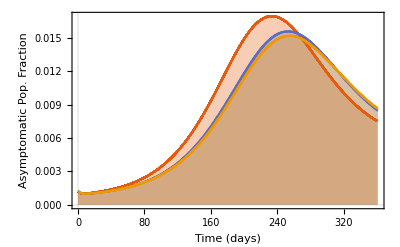

```mathematica
pltnIA =
ListStepPlot[
Thread[{tvecNC,nIS}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Asymptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Asymptomatic Pop. Fraction",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltIA =
ListStepPlot[
Thread[{tvecC,IA}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Asymptomatic Pop. Fraction",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltNLNVncIA =
ListStepPlot[
{
tsnlnvIA,
Thread[{tvecC,nIA}],
Thread[{tvecC,IA}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Asymptomatic Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Asymptomatic Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotTheme->strTheme
]
```

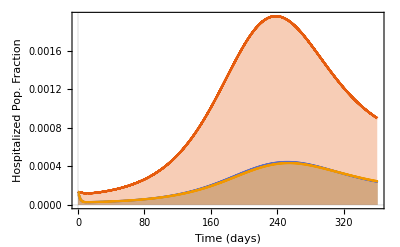

```mathematica
pltnH=
ListStepPlot[
Thread[{tvecNC,nH}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Death (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltH =
ListStepPlot[
Thread[{tvecC,H}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Hospitalized Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Hospitalized Pop. Fraction",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotRange->{{0,360}, {0.0, 0.008}},
PlotTheme->strTheme
];
pltNLNVncH =
ListStepPlot[
{
tsnlnvH,
Thread[{tvecC,nH}],
Thread[{tvecC,H}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Hospitalized Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Hospitalized Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotTheme->strTheme,
ImageSize->400
]
```

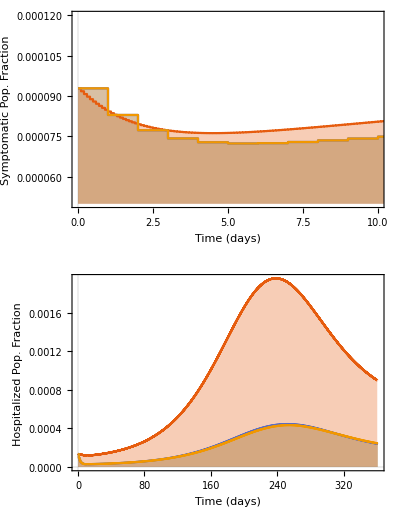

VaccinationEffect.pdf

```mathematica
FigVaccinationEffect = GraphicsGrid[
{
{pltNLNVncIS} , 
{pltNLNVncH}
}]
Export["VaccinationEffect.pdf",FigVaccinationEffect]
```

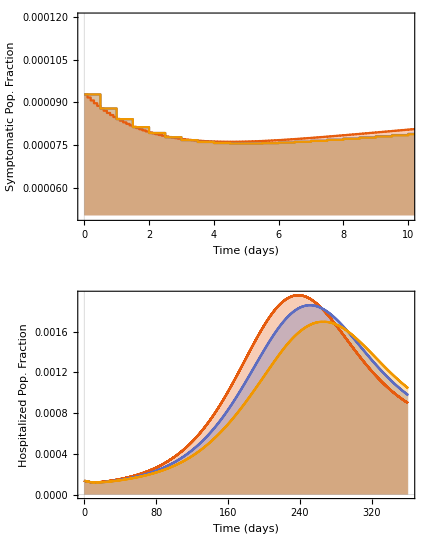

-Graphics-

```mathematica
Export["/home/gabrielsalcedo/Documentos/UNISON-UADY-Project/programas_240/VaccinationEffect2.pdf",FigVaccinationEffect,"PDF"];
```

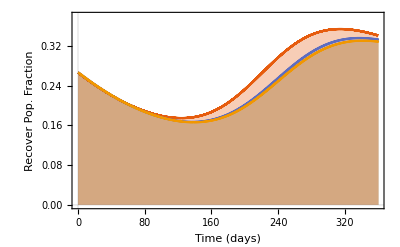

```mathematica
pltnR =
ListStepPlot[
Thread[{tvecNC,nR}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Recover Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Recover Pop. Fraction",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltR =
ListStepPlot[
Thread[{tvecC,R}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Recover Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Recover Pop. Fraction",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltNLNVncR =
ListStepPlot[
{
tsnlnvR,
Thread[{tvecC,nR}],
Thread[{tvecC,R}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Recover Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Recover Pop. Fraction",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotRange->{{0, 360}, {0.0,.38}},
PlotTheme->strTheme
]
```

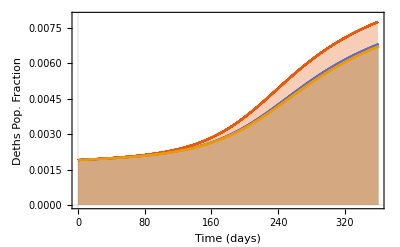

```mathematica
pltnD =
ListStepPlot[
Thread[{tvecNC,nDcov}],
PlotStyle->{Thick,Red},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Death (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotTheme->strTheme
];
pltD =
ListStepPlot[
Thread[{tvecC,Dcov}],
PlotStyle->{Thick,Blue},
AxesLabel->{"Time(days)", "Death Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Death (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotRange->{{0,360}, {0.0, 0.008}},
PlotTheme->strTheme
];
pltNLNVncD =
ListStepPlot[
{
tsnlnvD,
Thread[{tvecC,nDcov}],
Thread[{tvecC,Dcov}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Deths Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Deths Pop. Fraction",None},
{"Time (days)", None}
},
PlotRange->{{0.0, 360}, {0.00,0.008}},
PlotTheme->strTheme,
FrameTicks->Automatic,
ImageSize->400
]
```

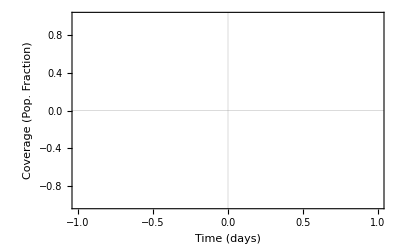

```mathematica
pltVc =
ListStepPlot[
Thread[{tvecC, Xcov}],
Filling->Axis,
AxesLabel->{"Time(days)", "Coverage (Pop. Fraction)"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Coverage (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotStyle->Gray,
ImageSize->400
]
pltnVc =
ListStepPlot[
Thread[{tvecNC, nXcov}],
Filling->Axis,
AxesLabel->{"Time(days)", "Coverage (Pop. Fraction)"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Coverage (Pop. Fraction)",None},
{"Time (days)", None}},
FrameTicks->Automatic,
PlotStyle->Gray,
ImageSize->400
];
pltncVcon =
ListStepPlot[
{
Thread[{tvecNC,nXcov}],
Thread[{tvecC,Xcov}]
},
PlotTheme->strTheme,
Filling->Axis,
AxesLabel->{"Time(days)", "Recover Pop. Fraction"},
Frame->{{True,False},{True,False}},
FrameLabel->{
{"Coverage (Pop. Fraction)",None},
{"Time (days)", None}
},
FrameTicks->Automatic,
PlotRange->{{0, 360}, {0.0,1}},
PlotTheme->strTheme];
```

Coverage

Here we implement the cumulative quadrature of

Interpolation::indat: Data point {t,0.000611352 (CIA+CL+CR+CS+ⅇ)} contains abscissa t, which is not a real number.

Interpolation::indat: Data point {t,(0.000611352+uV) (CIA+CL+CR+CS+ⅇ)} contains abscissa t, which is not a real number.

NIntegrate::inumr: The integrand Interpolation[{{t,0.000611352 (CIA+CL+CR+CS+ⅇ)},{0.,0.00227147},{1.,0.00227124},{2.,0.00227102},{3.,0.0022708},{4.,0.00227063},{5.,0.00227065},{6.,0.00227068},{7.,0.00227071},{8.,0.00227064},«32»,{41.,0.00225874},{42.,0.0022591},{43.,0.00225946},{44.,0.00225967},{45.,0.00225909},{46.,0.00225852},{47.,0.00225795},{48.,0.00225736},«312»}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.00735429}}.

NIntegrate::inumr: The integrand Interpolation[{{t,0.000611352 (CIA+CL+CR+CS+ⅇ)},{0.,0.00227147},{1.,0.00227124},{2.,0.00227102},{3.,0.0022708},{4.,0.00227063},{5.,0.00227065},{6.,0.00227068},{7.,0.00227071},{8.,0.00227064},«32»,{41.,0.00225874},{42.,0.0022591},{43.,0.00225946},{44.,0.00225967},{45.,0.00225909},{46.,0.00225852},{47.,0.00225795},{48.,0.00225736},«312»}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.00735429}}.

NIntegrate::inumr: The integrand Interpolation[{{t,0.000611352 (CIA+CL+CR+CS+ⅇ)},{0.,0.00227147},{1.,0.00227124},{2.,0.00227102},{3.,0.0022708},{4.,0.00227063},{5.,0.00227065},{6.,0.00227068},{7.,0.00227071},{8.,0.00227064},«32»,{41.,0.00225874},{42.,0.0022591},{43.,0.00225946},{44.,0.00225967},{45.,0.00225909},{46.,0.00225852},{47.,0.00225795},{48.,0.00225736},«312»}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7.35429}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

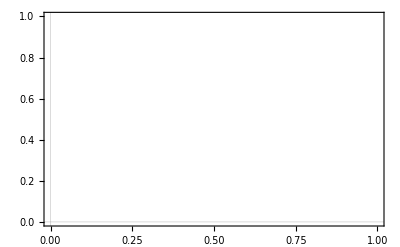

NIntegrate::inumr: The integrand Interpolation[{{t,(0.000611352+uV) (CIA+CL+CR+CS+ⅇ)},{0.,0.00262947},{1.,0.00262921},{2.,0.00262895},{3.,0.0026287},{4.,-0.000441893},{5.,-0.000441898},{6.,-0.000441903},{7.,-0.000441908},«33»,{41.,-0.00381379},{42.,-0.0038144},{43.,-0.00381501},{44.,0.00730649},{45.,0.00730463},{46.,0.00730278},{47.,0.00730093},{48.,0.00828171},«312»}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.00735429}}.

NIntegrate::inumr: The integrand Interpolation[{{t,(0.000611352+uV) (CIA+CL+CR+CS+ⅇ)},{0.,0.00262947},{1.,0.00262921},{2.,0.00262895},{3.,0.0026287},{4.,-0.000441893},{5.,-0.000441898},{6.,-0.000441903},{7.,-0.000441908},«33»,{41.,-0.00381379},{42.,-0.0038144},{43.,-0.00381501},{44.,0.00730649},{45.,0.00730463},{46.,0.00730278},{47.,0.00730093},{48.,0.00828171},«312»}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.00735429}}.

NIntegrate::inumr: The integrand Interpolation[{{t,(0.000611352+uV) (CIA+CL+CR+CS+ⅇ)},{0.,0.00262947},{1.,0.00262921},{2.,0.00262895},{3.,0.0026287},{4.,-0.000441893},{5.,-0.000441898},{6.,-0.000441903},{7.,-0.000441908},«33»,{41.,-0.00381379},{42.,-0.0038144},{43.,-0.00381501},{44.,0.00730649},{45.,0.00730463},{46.,0.00730278},{47.,0.00730093},{48.,0.00828171},«312»}][s] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,7.35429}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

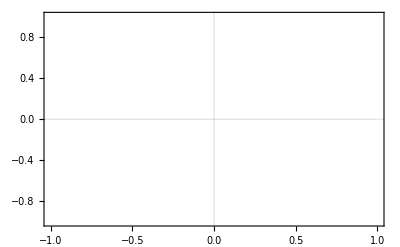

```mathematica
ToExpression[
"x_{vac}(t) = \\int_{0}^{t} (\\lambda_{V} + u_V)(L + S + EE + A + R) \\, dx",
TeXForm, HoldForm];
doseT = Interpolation[
Thread[{tControl,0.0006113521953813965 * (L + S + E + IA + R)}]
];
ControlledDoseT = Interpolation[
Thread[{tControl,uV * (L + S + E + IA + R)}]
];
xCov[t_]:=NIntegrate[doseT[s],{s,0, t}];
ControlledxCov[t_]:=NIntegrate[ControlledDoseT [s],{s,0, t}];
p1 = Plot[xCov[t], {t, 0, 360}]
p2 = Plot[ControlledxCov[t], {t, 0, 360}]
pp1 = ListLinePlot[
{Thread[{tControl, Xcov}],
Thread[{tControl, nXcov}]},
PlotTheme->strTheme,
Filling->Axis
]
```

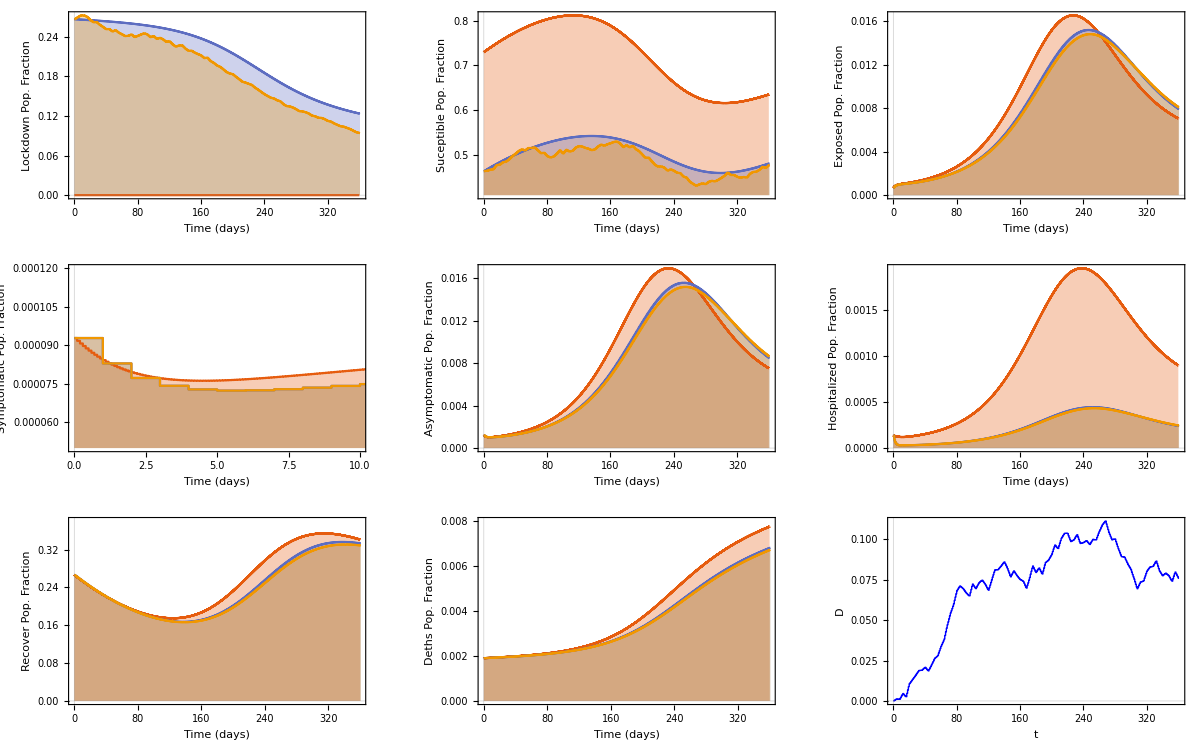

```mathematica
(*Controlled dynamics*)
GraphicsGrid[
{
{pltNLNVncL,pltNLNVncS, pltNLNVncE},
{pltNLNVncIS,pltNLNVncIA, pltNLNVncH},
{pltNLNVncR,pltNLNVncD, plotdatC[9]}
}
]
```

```mathematica
Her we need to run the dynamics without vaccination
```

dynamics Her need run the to vaccination we without

Part::partw: Part 11 of {NCL,NCS,NCE,NCIS,NCIA,NCH,NCR,NCD,NCV,} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

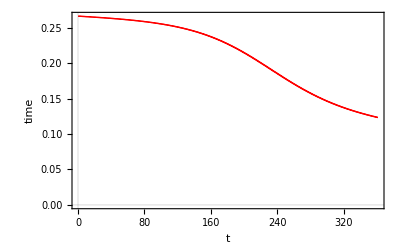
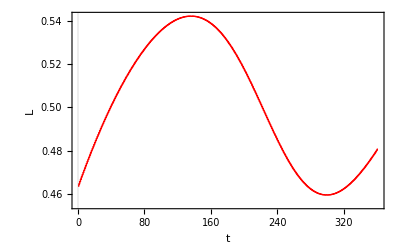
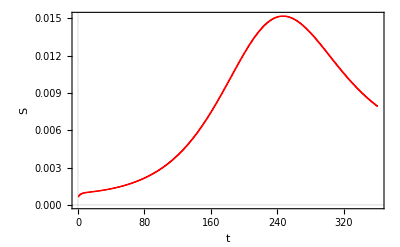
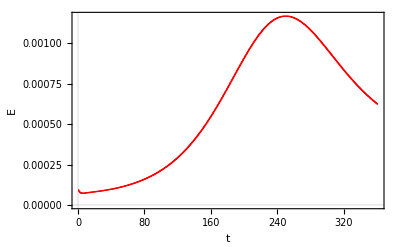
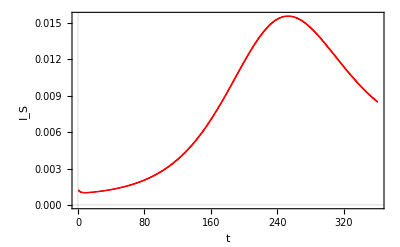
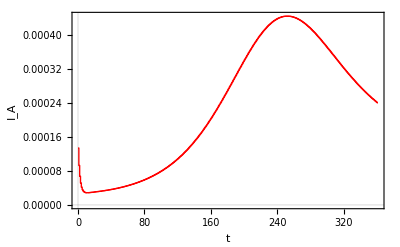
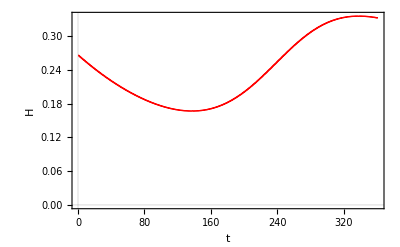
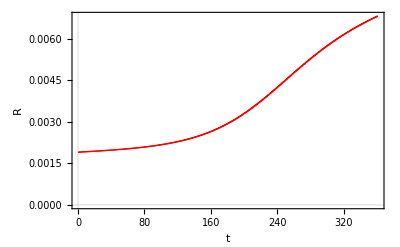

Part::partw: Part 11 of {t,CL,CS,CE,CIS,CIA,CH,CR,CD,CV} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

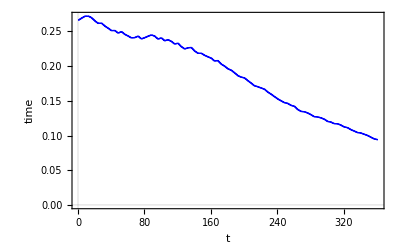
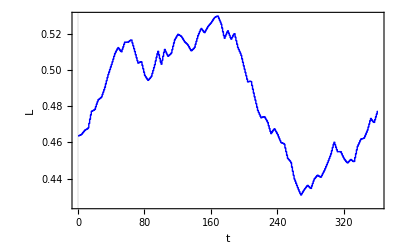
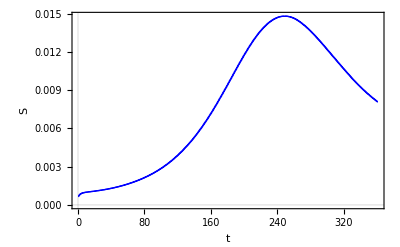
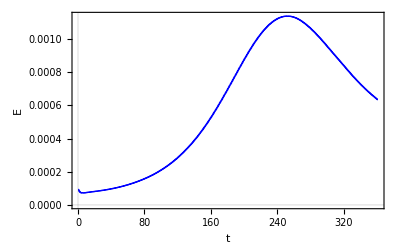
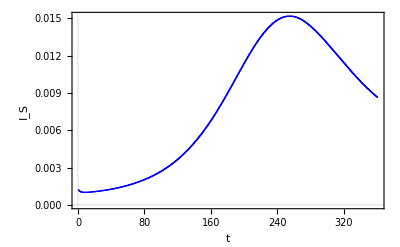
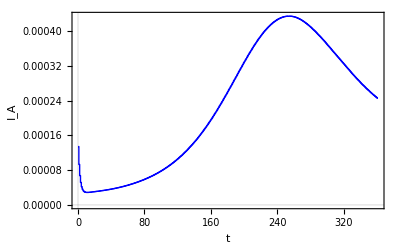
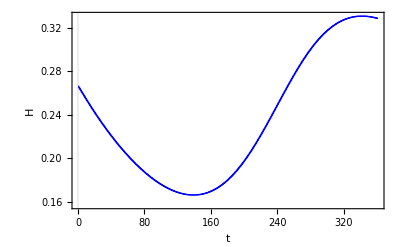
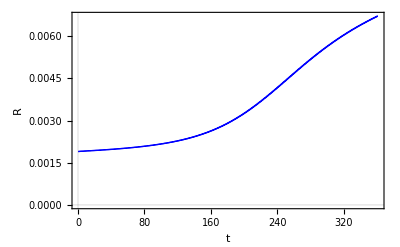

```mathematica
(*Clases NO optimized*)
Table[plotdatNC[k],{k,1,dim-1}]
Table[plotdatC[k],{k,1,dim-1}]
```

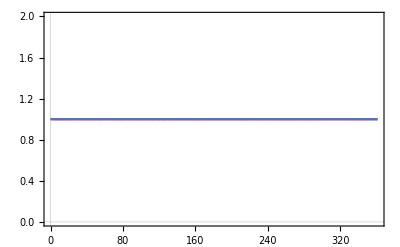

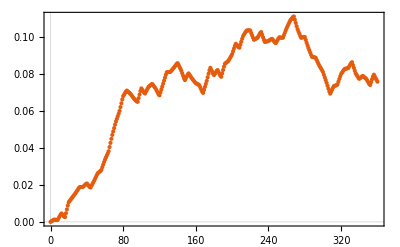

14

```mathematica
cl = L + S +Ex + IS + IA + H + R + Dcov+V;
ncl = nL + nS +nEx + nIS + nIA + nH + nR + nDcov + nV;
pltcCL = ListStepPlot[
{
Thread[{tvecNC,cl}],
Thread[{tvecC,ncl}]
}
]
pltnV = ListPlot[Thread[{tvecNC, V}]]
dim
```